```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
```

```mathematica
Logγ[Expγ[y]] // PowerExpand // FullSimplify
```

y

```mathematica
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

```mathematica
X0 = 2;
Clear[X0]
x[t_, g_] := X0 ⊗ Expγ[Logγ[g] t];
```

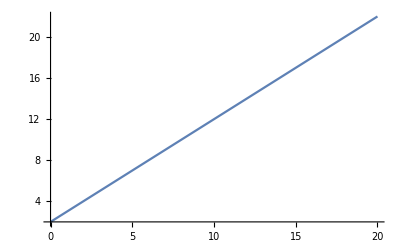

```mathematica
Plot[x[t,2] /. {X0->2, γ->1}, {t, 0, 20}, PlotRange->Full]
```

```mathematica
x[3,g +1] /. γ-> 0 // PowerExpand // FullSimplify
```

(1+g)^3 X0

```mathematica
(Log[(g+r)/(g-r)]/Log[g^2- r^2])^2 /. {g->21/20, r-> 9/20} // N
```

75.6329